```mathematica
raw=Import["C:/Users/gram/Documents/GitHub/smoothie/20160510_list.txt","Data"];
```

```mathematica
raw//Length
```

70

```mathematica
raw[[1]]
```

{Almond Mocha High Protein,345,9,1,80,51,42,37,30,195,2}

```mathematica
labels=raw[[All,1]];
```

```mathematica
sugar=Table[raw[[i,8]],{i,1,Length[raw]}];
```

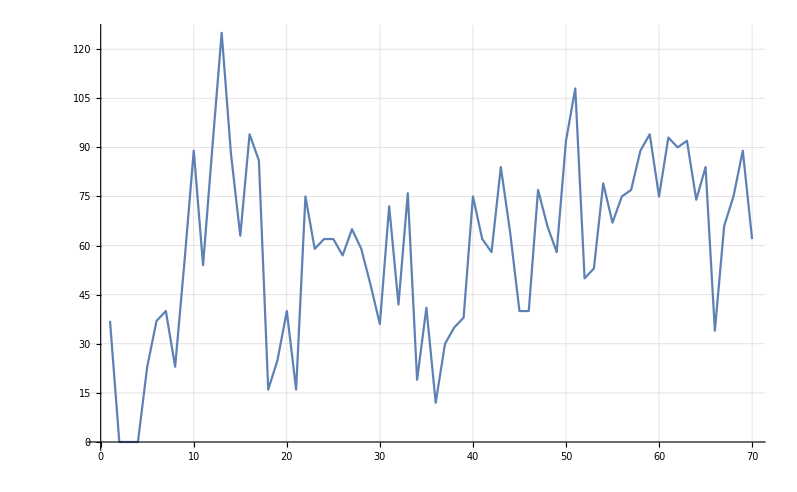

```mathematica
ListPlot[sugar,Joined->True,GridLines->Automatic]
```

So the lowest sugar smoothies are 2,3,4,18,21,34,36

```mathematica
labels[[{2,3,4,18,21,34,36}]]
```

{Gladiator® Chocolate,Gladiator® Strawberry,Gladiator® Vanilla,Lean1™ Chocolate,Lean1™ Vanilla,The Shredder - Chocolate™,The Shredder - Vanilla™}

```mathematica
proSugIndex=raw[[All,9]]/raw[[All,8]]//N
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{0.810811,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17391,0.810811,0.65,1.17391,0.345455,0.213483,0.333333,0.266667,0.2,0.261364,0.380952,0.159574,0.127907,1.1875,0.64,0.425,1.1875,0.0533333,0.186441,0.177419,0.193548,0.210526,0.0461538,0.,0.3125,0.194444,0.111111,0.166667,0.0131579,1.52632,0.731707,3.,0.6,0.314286,0.263158,0.0666667,0.016129,0.0172414,0.,0.109375,0.1,0.2,0.0649351,0.0454545,0.0344828,0.0108696,0.00925926,0.,0.0566038,0.0126582,0.134328,0.0533333,0.155844,0.011236,0.0106383,0.0666667,0.0107527,0.0444444,0.076087,0.0135135,0.047619,0.382353,0.136364,0.12,0.011236,0.016129}

```mathematica
proSugIndex[[{2,3,4}]]=1.8
```

1.8

```mathematica
proSugIndex
```

{0.810811,1.8,1.8,1.8,1.17391,0.810811,0.65,1.17391,0.345455,0.213483,0.333333,0.266667,0.2,0.261364,0.380952,0.159574,0.127907,1.1875,0.64,0.425,1.1875,0.0533333,0.186441,0.177419,0.193548,0.210526,0.0461538,0.,0.3125,0.194444,0.111111,0.166667,0.0131579,1.52632,0.731707,3.,0.6,0.314286,0.263158,0.0666667,0.016129,0.0172414,0.,0.109375,0.1,0.2,0.0649351,0.0454545,0.0344828,0.0108696,0.00925926,0.,0.0566038,0.0126582,0.134328,0.0533333,0.155844,0.011236,0.0106383,0.0666667,0.0107527,0.0444444,0.076087,0.0135135,0.047619,0.382353,0.136364,0.12,0.011236,0.016129}

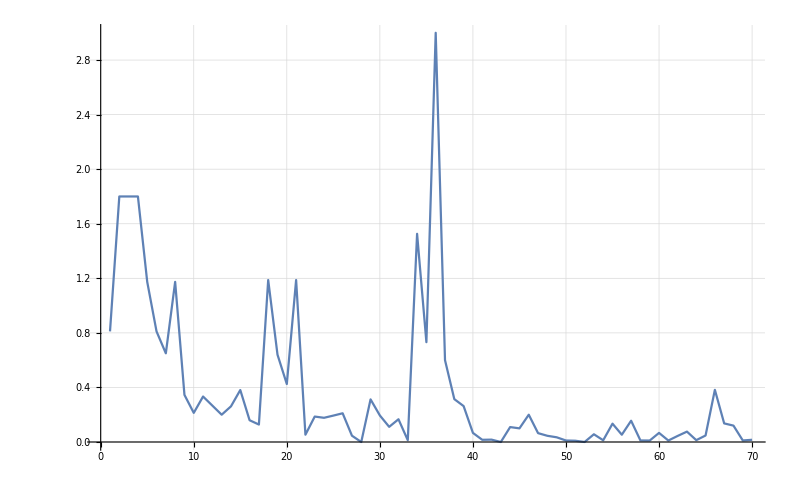

```mathematica
ListPlot[proSugIndex,Joined->True,GridLines->Automatic,PlotRange->All]
```

```mathematica
Position[proSugIndex,3.0]
```

{{36}}

```mathematica
labels[[36]]
```

The Shredder - Vanilla™

```mathematica
normal = raw/. 0->.001;
normal=Table[Table[normal[[i,j]]/Max[normal[[All,j]]],{j,2,Length[normal[[1]]]}],{i,1,Length[normal]}]//N;
nutritionIndex=(normal[[All,6]]*normal[[All,8]]*normal[[All,10]])/(normal[[All,5]]*normal[[All,7]])
```

{0.206993,6974.92,6974.92,6974.92,0.517559,0.206993,0.09851,0.234519,1.63068,3.97074,2.47259,0.495994,0.413329,0.238969,1.38878,24.9316,1.15384,13.9886,5.41626,4.26865,8.50359,4.16635,2.05176,1.92498,2.18998,4.76416,0.0870375,0.18915,0.285611,0.000126034,0.657568,0.373405,1003.41,0.189261,1.73213,0.000634084,35153.6,37509.6,13949.8,0.633771,339.996,908.61,0.671659,0.225012,0.464995,0.201498,5374.61,2451.79,1603.43,316.736,503.744,0.322396,0.310581,745.561,0.512188,0.592438,0.34853,1013.58,479.835,5.20794,319.996,2.59019,0.446003,720.532,0.332139,0.000123916,0.000133862,0.199948,1034.48,502.494}

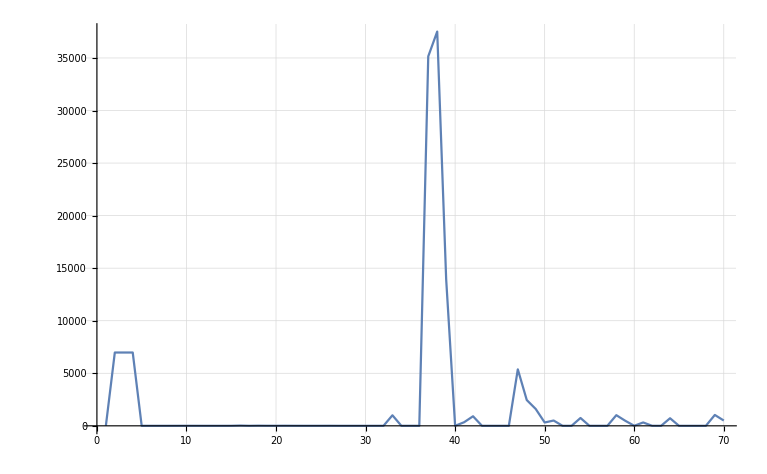

```mathematica
ListPlot[nutritionIndex,Joined->True,GridLines->Automatic,PlotRange->All]
```

```mathematica
normal[[{37,38}]]//TableForm
```

0.456432 | 0.65625 | 0.230769 | 0.664336 | 0.000011236 | 0.372414 | 0.24 | 0.4 | 0.388514 | 0.636364
0.33195 | 0.15625 | 0.153846 | 0.13986 | 0.000011236 | 0.482759 | 0.28 | 0.244444 | 0.194257 | 1.

```mathematica
labels[[{37,38}]]
```

{Vegan - Nutty Super Grain,Vegan - Dark Chocolate Banana}